## Inverse image function

December 2013

This Mathematica notebook is licensed under a  .
It provides software for producing the inverse image of an interval under a particular function.  I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework.

### Initial definitions

```mathematica
setup[f_,a_,b_,x_]:=Reduce[(f[x]≥a)&&(f[x]≤b),x,Reals]//Quiet(*Find interval(s)that make up inverse image*)
```

```mathematica
mint[{x_,y_}]:={{x,0},{y,0}}  (*Produces input for ListLinePlot*)
```

### The Main function

```mathematica
showinvimg[f_,xl0_,xr0_,astart0_,bstart0_,step0_,yb0_,yt0_,ar0_,vthick0_:0.01,ycolor0_:RGBColor[.7,.2,0],xcolor0_:RGBColor[.2,.6,0]]:=
Module[{xl=xl0,xr=xr0,astart=astart0,bstart=bstart0,step=step0,yb=yb0,yt=yt0,vthick=vthick0,ycolor=ycolor0,xcolor=xcolor0,ar=ar0},
Manipulate[
Show[
(*Plot function*)
Plot[
f[x],{x,xl,xr},PlotStyle->{Blue},PlotRange->{yb,yt},AspectRatio->ar
],
(*Plot output interval*)
If[a<b, (*Don't draw reversed intervals*)
ListLinePlot[
{{0,a},{0,b}},PlotStyle->{{ycolor,Thickness[vthick]}}
],
Plot[{},{x,xl,xr} ] (*Kludge necessary because "If" would produce "Null" here and Show[null] gives an error messages.*)
],
(*Show inverse image of output interval*)
If[a<b,
ListLinePlot[
If[Depth[setup[f,a,b,x]]<3, 
(*If Depth < 3, the setup function shows a single inequality, not as a list, so I have to put parentheses around it,  If it is ≥3, it shows a list of inequalities so the outer parentheses are already there*)
{mint @{setup[f,a,b,x][[1]],setup[f,a,b,x][[-1]]}},mint @{setup[f,a,b,x][[#]][[1]],setup[f,a,b,x][[#]][[-1]]}&/@Table[
i,{i,Length[setup[f,a,b,x]]}]
],
PlotStyle->{{xcolor,Thickness[vthick]}}],
Plot[{},{x,xl,xr}]
]
],
{{a,astart},yb,yt,step,Appearance->{"Labeled","Open"}},{{b,bstart},yb,yt,step,Appearance->{"Labeled","Open"}},SaveDefinitions->True]
]
```

### Examples

```mathematica
cu[x_]:=x^3-x
```

```mathematica
showinvimg[cu,-1.7,1.7,-1.0,1.0,.05,-1.7,1.7,1.0,0.01]
```

#### Parabola

```mathematica
qu[x_]:=x^2-1
```

```mathematica
showinvimg[qu,-1.8,1.8,-0.5,1.2,.05,-1.05,2.25,3.6/3.3]
```

#### Quartic

```mathematica
qf[x_]:=x (.75x-1) (x-2) (1.1x+1)
```

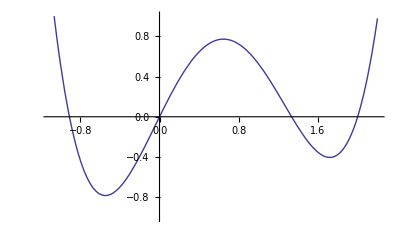

```mathematica
Plot[qf[x],{x,-1.1,2.2},PlotRange->{-1,1},AspectRatio->2/3.3]
```

```mathematica
showinvimg[qf,-1.1,2.2,-.3,.75,.05,-1,1,4/8.4]
```

#### Quintic

```mathematica
ff[x_]:=-.5+.5x+.2x^2-.19x^3-.015x^4+.01x^5
```

```mathematica
Manipulate[setup[ff,a,b,x],{{a,-1},-2,2,.05,Appearance->{"Labeled","Open"}},{{b,1},-2,2,.05,Appearance->{"Labeled","Open"}}]
```

```mathematica
Manipulate[setup[ff,a,b,x]//TreeForm,{{a,-1},-2,2,.05,Appearance->{"Labeled","Open"}},{{b,1},-2,2,.05,Appearance->{"Labeled","Open"}}]
```

```mathematica
showinvimg[ff,-4.1,4.3,-1.4,1,.05,-2,2,4/8.4]
```